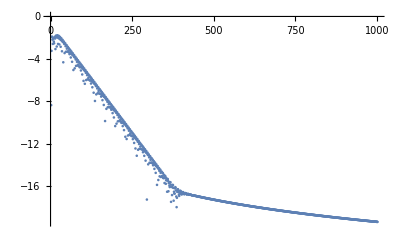

{0.809963-0.0942554 ⅈ,-0.809963-0.0942554 ⅈ,0.-0.190862 ⅈ,1.31509-0.191338 ⅈ,-1.31509-0.191338 ⅈ,0.797156-0.284499 ⅈ,-0.797156-0.284499 ⅈ,0.-0.902866 ⅈ}

```mathematica
data$raw=Import["psi4_I.csv"];
data$raw=data$raw[[2;;-1,1]];
ListPlot[Log10[Abs[data$raw]],PlotRange->All]
data=data$raw[[50;;-1]];
n=Length[data];
p=8;
X=Table[data[[(j);;(j+p-1)]],{j,1,n-p}];
Y=Table[data[[(j+1);;(j+p)]],{j,1,n-p}];
(* QNM *)
Sort[I*Log@Eigenvalues[PseudoInverse[X].Y],Im[#1]>Im[#2]&]
```

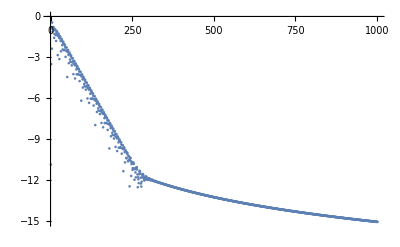

{0.657536-0.09572 ⅈ,-0.657536-0.09572 ⅈ,0.-0.164376 ⅈ,0.643009-0.29032 ⅈ,-0.643009-0.29032 ⅈ,0.599001-0.465452 ⅈ,-0.599001-0.465452 ⅈ,0.-0.629129 ⅈ}

```mathematica
data$raw=Import["phi2_I.csv"];
data$raw=data$raw[[2;;-1,1]];
ListPlot[Log10[Abs[data$raw]],PlotRange->All]
data=data$raw[[28;;-1]];
n=Length[data];
p=8;
X=Table[data[[(j);;(j+p-1)]],{j,1,n-p}];
Y=Table[data[[(j+1);;(j+p)]],{j,1,n-p}];
Sort[I*Log@Eigenvalues[PseudoInverse[X].Y],Im[#1]>Im[#2]&]
```